## Drawing Homer with epicycles (July 6, 2018)

This notebook is really just a tweak of the following contribution by “anderstood” on the Mathematica stackexchange:
https://mathematica.stackexchange.com/questions/171755/how-can-i-draw-a-homer-with-epicycloids
It supplements a discussion in my Mathologer video “Epicycles, complex Fourier and Homer Simpson’s orbit”.

Enjoy, burkard

Here we go. First we read in the single pixel outline of Homer that I mention in the video and make a list of the coordinates of the black pixels in this picture (pts is this list).

```mathematica
img=Import["http://www.qedcat.com/misc/homer1_clean_pixel.png"];
pts=PixelValuePositions[img, Black,0.05];
```

-Graphics-

We shift the coordinates so that the origin of our coordinate system comes to rest roughly in the centre of the image. Then we order the list by creating a (close to shortest) roundtrip though the points using the command FindShortestTour. The rest of the file works exactly as described by anderstood (except I also fixed up the wrongly placed centres of the epicycles).

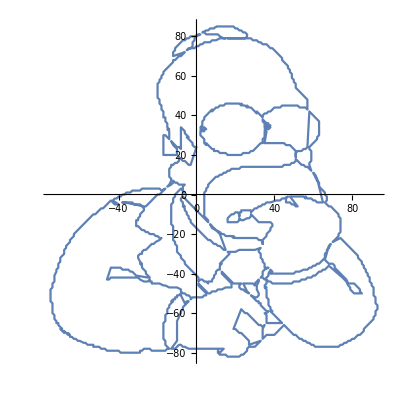

```mathematica
pts=Map[{-90,-90}+#&,pts];
elephantPlot=ListPlot[pts,AspectRatio->Automatic];
shortest=Last@FindShortestTour@pts;
pts=pts[[shortest]];
ListLinePlot[pts,AspectRatio->Automatic]
```

The following is a preview of what 900 epicycles will eventually draw.

```mathematica
SetAttributes[toPt,Listable]
toPt[z_]:=ComplexExpand[{Re@z,Im@z}]//Chop;
cf=Compile[{{z,_Complex,1}},Module[{n=Length@z},1/n*Table[Sum[z[[k]]*Exp[-I*i*k*2 Pi/n],{k,1,n}],{i,-m,m}]]];
z=pts[[All,1]]+I*pts[[All,2]];
m=450
cn=cf[z];
{f[t_],g[t_]}=Sum[cn[[j]]*Exp[I*(j-m-1)*t],{j,1,2 m+1}]//toPt;
ParametricPlot[{f[t],g[t]},{t,0,2 Pi},PlotStyle->Thickness[0.01],AspectRatio->Automatic]
```

450

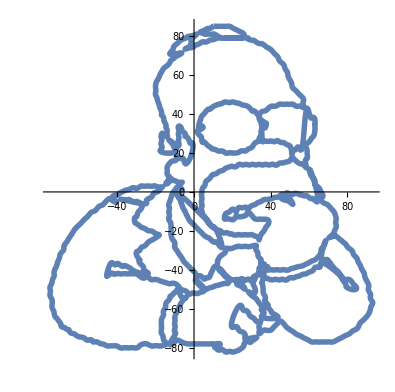

```mathematica
FourierSeries
```

Here we go. I actually only include a preview of the animation in this notebook to keep the file size reasonably small.
If you’ve got access to Mathematica just generate the animation yourself. If your computer is struggling with 
900 epicycles, just lower the m=450 above to something smaller. Apart from that, if you are just interested in making a silhouette just
use anderstood’s code together with my center position fix (spot the difference :)

```mathematica
r=Abs/@cn;
theta=Arg/@cn;
index={m+1}~Join~Riffle[Range[m+2,2 m+1],Reverse[Range[1,m]]];
p[t_]=Accumulate@Table[cn[[j]]*Exp[I*(j-m-1)*t],{j,index}]//toPt;
circles[t_]=Table[Circle[p[t][[i-1]],r[[index[[i]]]]],{i,1,2 m+1}];
anims=ParallelTable[ParametricPlot[{f[s],g[s]},{s,0,t},AspectRatio->Automatic,Axes->{False,False}, Epilog->{circles[t][[2;;]],Line[p[t]],Point[p[t]]},PlotRange->{{-100,100},{-100,100}},ImageSize->500],{t,Subdivide[0.1,4 Pi,400]}];ListAnimate@anims
```